```mathematica
Simplify[a^(n-1)/(2^(n/2-1)Gamma[n/2] σ^n)Exp[-a^2/(2 σ^2)]//.n->2,σ>0]
```

(a ⅇ^(-a^2/(2 σ^2)))/σ^2

```mathematica
Assuming[σ>0,Integrate[(a ⅇ^(-a^2/(2 σ^2)))/σ^2,{a,0,Infinity}]]
```

1

```mathematica
Clear[p]
```

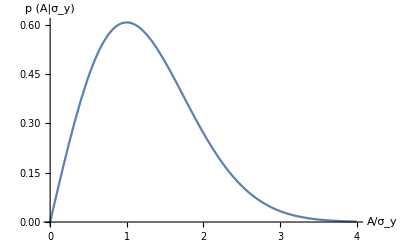

```mathematica
plot= Plot[(a Exp[-(a^2/(2 σ^2))])/σ^2/. σ->1,{a,0,4},AxesLabel->{TraditionalForm[A/Subscript[σ,y]],TraditionalForm[p(A|Subscript[σ,y])]}]
```

```mathematica
Export["~/Desktop/a-prior.pdf",plot]
```

~/Desktop/a-prior.pdf